Attempt to find likelihood of DM model

Note: input mass of dark matter in GeV since that is what PPPC uses.

PPPC mass of DM range 5 GeV -> 100TeV

#### Make spectral file of model

Define dN/dE for b-bbar that gets the flux of photons given the mass of dark matter (mdm) and ratio x (where x = E/mdm).

```mathematica
Get["/Users/austingottfredson/Indirect-Dark-Matter-Detection/dlNdlxEW.m"];
```

```mathematica
primary="b";
dnde[mdm_,x_,primary_]:=10^(dlNdlxIEW[primary->"γ"][mdm,Log[10,x]])/(Log[10]);
```

Use specfile if you want a spectrum plot for a given mass of DM.

```mathematica
specfile[mdm_]:=With[{i:=10^xp},Table[{i*mdm,dnde[mdm,i,primary]},{xp,-7,0,.2}]];
```

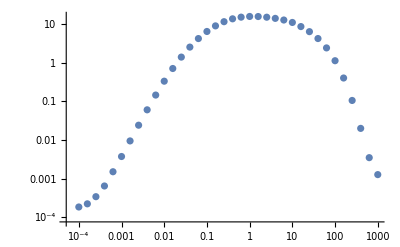

```mathematica
ListLogLogPlot[specfile[1000]]
```

#### Predict normalized energy of model for one energy bin

Import likelihood file and separate the columns

Column 1 -> url to galaxy data, column 2 -> J-Factor of galaxy, column 3 -> uncertainty of J-Factor

```mathematica
galaxies={{"http://www-glast.stanford.edu/pub_data/1048/like_bootes_I.txt",18.8,.22},{"http://www-glast.stanford.edu/pub_data/1048/like_canes_venatici_II.txt",17.9,.25},{"http://www-glast.stanford.edu/pub_data/1048/like_carina.txt",18.1,.23},{"http://www-glast.stanford.edu/pub_data/1048/like_coma_berenices.txt",19.0,.25},{"http://www-glast.stanford.edu/pub_data/1048/like_draco.txt",18.8,.16},{"http://www-glast.stanford.edu/pub_data/1048/like_fornax.txt",18.2,.21},{"http://www-glast.stanford.edu/pub_data/1048/like_hercules.txt",18.1,.23},{"http://www-glast.stanford.edu/pub_data/1048/like_leo_II.txt",17.6,.18},{"http://www-glast.stanford.edu/pub_data/1048/like_leo_IV.txt",17.9,.28},{"http://www-glast.stanford.edu/pub_data/1048/like_sculptor.txt",18.6,.18},{"http://www-glast.stanford.edu/pub_data/1048/like_segue_1.txt",19.5,.29},{"http://www-glast.stanford.edu/pub_data/1048/like_sextans.txt",18.4,.27},{"http://www-glast.stanford.edu/pub_data/1048/like_ursa_major_II.txt",19.3,.28},{"http://www-glast.stanford.edu/pub_data/1048/like_ursa_minor.txt",18.8,.19},{"http://www-glast.stanford.edu/pub_data/1048/like_willman_1.txt",19.1,.31}};
```

```mathematica
likefile="http://www-glast.stanford.edu/pub_data/1048/like_hercules.txt";
data[likefile_]:=Import[likefile,"Table"];
data2[likefile_]:=Drop[data[likefile],2];
emins[likefile_]:=Flatten[DeleteDuplicates[data2[likefile][[All,1]]]];
emaxs[likefile_]:=Flatten[DeleteDuplicates[data2[likefile][[All,2]]]];
efluxeslikes[likefile_]:=data2[likefile][[All,{1,3,4}]];
loglikes[likefile_]:=Flatten[data2[likefile][[All,4]]];
```

Integrate a generic spectrum, multiplied by E, to get the energy flux. Multiply by 1000 to change from GeV to MeV. The units will just be MeV for an energy bin with a given emin and emax. This is normalized per sing dark matter annihilation.

```mathematica
pred[mdm_,ebin_,primary_,likefile_]:=NIntegrate[dnde[mdm,energy/mdm,primary],{energy,emins[likefile][[ebin]]/1000,emaxs[likefile][[ebin]]/1000.}]*1000.;
```

#### Eq. 1 from Fermi analysis for one energy bin

Define J factor

```mathematica
jfactor=10^18.1;
```

eflux in MeV/cm^2/s

```mathematica
eflux[sigmav_,mdm_,ebin_,primary_,jfactor_]:=sigmav/(8*Pi*(mdm^2))*pred[mdm,ebin,primary,likefile]*jfactor
```

#### Plot for eflux vs ⟨σv⟩

```mathematica
efluxplot=With[{i:=10^xp},Table[{i,eflux[i,1000.,1,primary,jfactor]},{xp,-30.,-20.,1.}]];
```

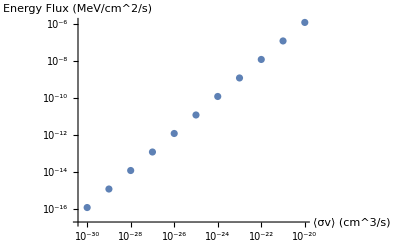

```mathematica
ListLogLogPlot[efluxplot,AxesLabel->{"⟨σv⟩ (cm^3/s)","Energy Flux (MeV/cm^2/s)"}]
```

#### Plot for Log-Likelihood vs mass of DM and sigma*v

Make a loop to separate efluxeslikes into each bin and then train interpolation.
1) separate efluxeslikes into bins
2) train interpolation for each energy bin
3) input eflux into interpolation to get deltaloglike for each energy bin
4) add deltaloglike of each energy bin together
5) Solve for

```mathematica
likebin[bin_,likefile_]:=(Join @@ SequenceCases[efluxeslikes[likefile],{{emins[likefile][[bin]],_,_}}])[[All,{2,3}]]
```

Train interpolation of likelihood file for each bin. The output is the Log-Likelihood.

```mathematica
likeinterp[sigmav_,mdm_,bin_,primary_,likefile_,jfactor_]:=Interpolation[likebin[bin,likefile],eflux[sigmav,mdm,bin,primary,jfactor]];
```

Find the likelihood given eflux found from the eflux function

```mathematica
(*Add together the deltaloglike of each bin given a DM mass and sigmav*)
like[sigmav_,mdm_,primary_,likefile_,jfactor_]:= Sum[likeinterp[sigmav,mdm,bin,primary,likefile,jfactor],{bin,1,24}]
(*Using the sum of each deltaloglike for each bin, find the value of sigmav that gives a (deltaloglike) = (loglike) - (loglikemax) = -2.71/2 *)
(*Return the maximum log like possible*)
loglikemax[mdm_,primary_,likefile_,jfactor_]:=like[10^-30,mdm,primary,likefile,jfactor];
(*Decide many galaxies to include with the Sum function*)sigv[mdm_,primary_]:=sv/.FindRoot[Sum[like[sv,mdm,primary,galaxies[[n,1]],galaxies[[n,2]]]-loglikemax[mdm,primary,galaxies[[n,1]],galaxies[[n,2]]],{n,1,1}]+2.71/2,{sv,10^-20,10^-30}]
(*Make a table to plot sigmav vs DM mass*)
sigmavplot[primary_]:= With[{i:=10^xp},Table[{i, sigv[i,primary]}, {xp, 2.6, 4, 4/20}]];
```

```mathematica
likeplot[mdm_,primary_]:=With[{sigv:=10^xp},Table[{sigv,Sum[like[sigv,mdm,primary,galaxies[[n,1]],galaxies[[n,2]]]-loglikemax[mdm,primary,likefile,jfactor],{n,1,1}]},{xp,-26,-20,.5}]]
```

```mathematica
(*Try plotting log-likelihood vs sigmav for a certain DM mass*)
likebbbar=likeplot[1000,primary];
```

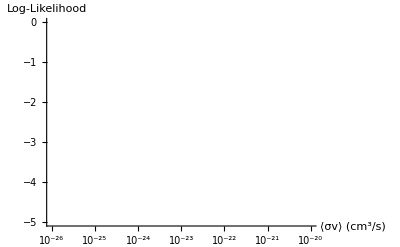

```mathematica
loglikelihood = ListLogLinearPlot[likebbbar,AxesLabel->{"⟨σv⟩ (cm^3/s)","Log-Likelihood"},FrameTicksStyle->Automatic];
c=LogLinearPlot[-2.71/2,{x,10^-26.5,10^-20},PlotPoints->40];
Show[loglikelihood,AxesLabel->{"⟨σv⟩ (cm^3/s)","Log-Likelihood"},FrameTicksStyle->Automatic,PlotRange->{-5,0}]
```

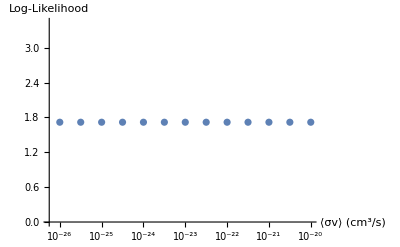

```mathematica
loglikelihood
```

```mathematica
likebbbar
```

{{1.×10^-26,1.71766},{3.16228×10^-26,1.71766},{1.×10^-25,1.71766},{3.16228×10^-25,1.71766},{1.×10^-24,1.71766},{3.16228×10^-24,1.71766},{1.×10^-23,1.71766},{3.16228×10^-23,1.71766},{1.×10^-22,1.71766},{3.16228×10^-22,1.71766},{1.×10^-21,1.71766},{3.16228×10^-21,1.71766},{1.×10^-20,1.71766}}

```mathematica
bbbarplot=sigmavplot[primary];
(*taoplot=sigmavplot["τ",likefile,jfactor];*)
```

$Aborted

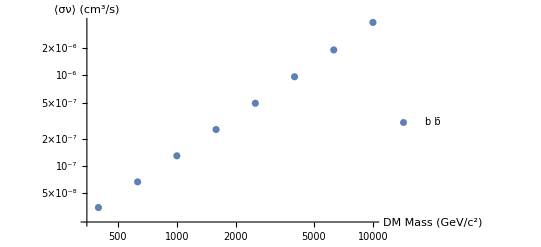

```mathematica
ListLogLogPlot[bbbarplot,AxesLabel->{"DM Mass (GeV/c^2)","⟨σν⟩ (cm^3/s)"},PlotLegends->{primary"b̄","τ^+τ^-"}]
```

```mathematica
Sum[like[10^-26,1000.,primary,galaxies[[n,1]],galaxies[[n,2]]]-loglikemax[1000.,primary,galaxies[[n,1]],galaxies[[n,2]]],{n,1,5}]+2.71/2
```

1.355

```mathematica
like[10^-8,1000.,primary,galaxies[[1,1]],galaxies[[1,2]]]
```

-1.47485

```mathematica
loglikemax[1000.,primary,galaxies[[1,1]],galaxies[[1,2]]]
```

-1.46513